### Setup: Clear, Units, Assumptions

```mathematica
(*Clear*)
Remove["Global`*"]

(*Units*)
μs=10^-6;
MHz=10^6;

(*Assumptions*)
PS=222 MHz;
PP=37 MHz;
Γ=100 MHz;
DS=0;
DP=0;
```

### Describe the System: Hamiltonian and Laser Pulses

Set::write: Tag Integer in 0[t] is Protected.

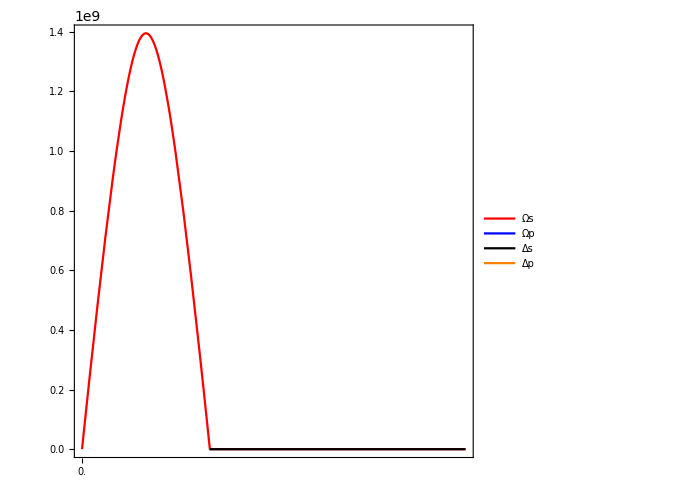

```mathematica
(*Hamiltonian: Λ structure*)
H=2π({{0, 1/2 Ωp[t], 1/2 Ωpp[t], 0}, {1/2 Ωp[t], Δp[t]-ⅈ Γ/2, 0, 1/2 Ωs[t]}, {1/2 Ωpp[t], 0, Δp[t]+(133.86-130.41)10^9-ⅈ Γ/2, 0}, {0, 1/2 Ωs[t], 0, Δp[t]-Δs[t]}});

(*Laser Pulses: in order of Ωs, Ωp, Δs, Δp *)
pulses={Piecewise[{{PS/(√1.3-√(.3))(√1.3-√(((t-w/2)/(w/2))^2+0.3)), 0<t<w}}],Piecewise[{{PP/(√1.3-√(.3))(√1.3-√(((t-t1-w/2)/(w/2))^2+0.3)), t1<t<t1+w}}],Piecewise[{{DS*(t-w/2)/w, 0<t<w}}],Piecewise[{{DP*(t-t1-w/2)/w, t1<t<t1+w}}]}; 
{Ωs[t],Ωp[t],Δs[t],Δp[t]}=pulses;
Plot[Evaluate[pulses],{t,0,15 μs},ImageSize->500,AspectRatio->1,Exclusions->None,PlotLegends->{"Ωs","Ωp","Δs","Δp"},PlotRange->All,FrameTicks->{Automatic,{{#,1000 #}&/@FindDivisions[{0.,.01},5]//N,Automatic}}]
```

### Eigenvalues

```mathematica
evalsByEnergy[H0_,t10_,w0_,DS0_,DP0_]:=Module[{H=H0,t1=t10,w=w0,DS=DS0,DP=DP0},
t1]
```

```mathematica
evalsByEnergy[H,5μs,10μs,0,0]
```

1/200000

```mathematica
ev=Eigenvalues[H,Quartics->True];
```

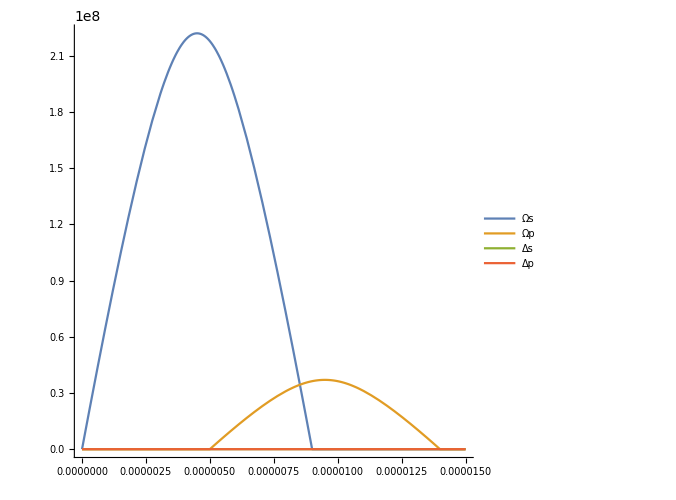

```mathematica
pulse2={Piecewise[{{PS/(√1.3-√(.3))(√1.3-√(((t-w/2)/(w/2))^2+0.3)), 0<t<w}}],Piecewise[{{PP/(√1.3-√(.3))(√1.3-√(((t-t1-w/2)/(w/2))^2+0.3)), t1<t<t1+w}}],Piecewise[{{DS*(t-w/2)/w, 0<t<w}}],Piecewise[{{DP*(t-t1-w/2)/w, t1<t<t1+w}}]}/.{w->9μs,t1->5μs,DS->0,DP->0};
Plot[Evaluate[pulse2],{t,0,15 μs},ImageSize->500,AspectRatio->1,Exclusions->None,PlotLegends->{"Ωs","Ωp","Δs","Δp"},PlotRange->All,FrameTicks->{Automatic,{{#,1000 #}&/@FindDivisions[{0.,.01},5]//N,Automatic}}]
```

```mathematica
w=9μs;t1=5μs;
```

```mathematica
Ωs[t_]=pulse2[[1]];
Ωp[t_]=pulse2[[2]];
Δs[t_]=pulse2[[3]];
Δp[t_]=pulse2[[4]];
```

```mathematica
ev1=ev/.Ωpp[t]->(1.7432+0.67256)/0.1897 Ωp[t];
ev2=ev/.Ωpp[t]->0;
```

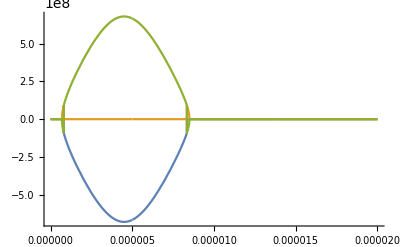

```mathematica
Show[Plot[Evaluate@Table[Re[ev2[[i]]],{i,1,3}],{t,0μs,20μs},PlotRange->All,ImageSize->400]]
```

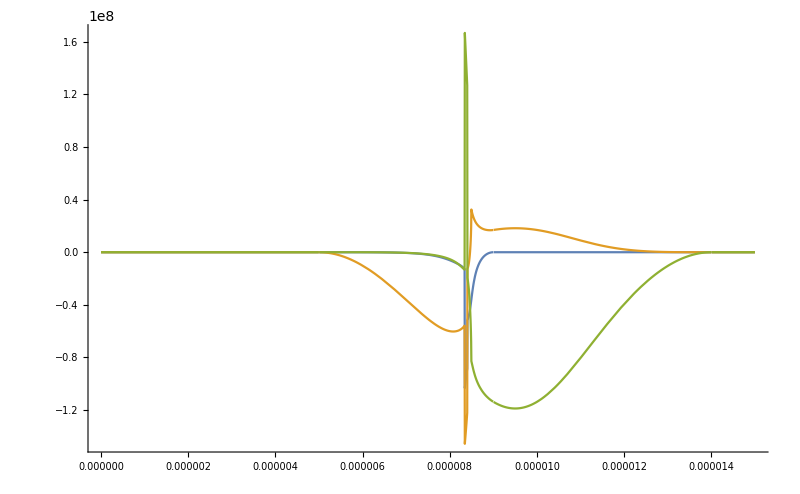

```mathematica
Plot[Evaluate@Table[Re[ev1[[i]]-ev2[[i]]],{i,1,3}],{t,0,15μs},PlotRange->All,ImageSize->800]
```

```mathematica
laserPlot[pulse_,w0_,t10_,DS0_,DP0_]:=Plot[Evaluate[pulse/.{w->w0,t1->t10,DS->DS0,DP->DP0}],{t,0,15 μs},ImageSize->500,AspectRatio->1,Exclusions->None,PlotLegends->{"Ωs","Ωp","Δs","Δp"},PlotRange->All]
```